# Rosseller: Sections

The plan is to just do all sorts of things myself.
See, https://en.wikipedia.org/wiki/R%C3%B6ssler_attractor#Varying_a
1) Cross standard section n times then stop. No sensitivities computed.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}};
CrossStdSection[f_,y0_,nMax_,TMax_:123, Δt0_:0.06]:=Module[
{n=1,y,t,tEnd,yEnd},
NDSolveValue[{y'[t]==f[y[t]],y[0]==y0},y,{t, 0, TMax},
StartingStepSize->Δt0,
Method->{"EventLocator",
Method->"ExplicitRungeKutta",
"Event":>f[y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>If[n++>=nMax,
yEnd=y[t];tEnd=t;"StopIntegration"]
}];
{n-1,tEnd,yEnd}]
PoincareReturn[f_,y0_,nMax_,TMax_:123, Δt0_:0.06]:=Module[
{n=1,y,t,tEnd,yEnd},
NDSolveValue[{y'[t]==f[y[t]],y[0]==y0},y,{t, 0, TMax},
StartingStepSize->Δt0,
Method->{"EventLocator",
Method->"ExplicitRungeKutta",
"Event":>f[y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>If[And[t>Δt0,n++>=nMax],
yEnd=y[t];tEnd=t;"StopIntegration"]
}];
{n-1,tEnd,yEnd}]
PoincareReturn[{f_,df_},y0_,nMax_,TMax_:123, Δt0_:0.06]:=Module[
{n=1,y,J,t,tEnd,yEnd,JEnd},
NDSolveValue[{y'[t]==f[y[t]],J'[t]==df[y[t]].J[t],
y[0]==y0,J[0]==IdentityMatrix[Length[y0]]},y,{t, 0, TMax},
StartingStepSize->Δt0,
Method->{"EventLocator",
Method->"ExplicitRungeKutta",
"Event":>f[y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>If[And[t>Δt0,n++>=nMax],
yEnd=y[t];tEnd=t;JEnd=J[t];"StopIntegration"]
}];
{n-1,tEnd,{yEnd,JEnd}}]
p={0.2,0.2,3.6};
yGuess={-3,-4,10};
{n0,t0,y0}=CrossStdSection[f[p],yGuess,5];
{n1,t1,Fy0}=PoincareReturn[f[p],y0,2];
{n1,t1,{Fy0,J0}}=PoincareReturn[{f[p],df[p]},y0,2];
(* Count maxes in z *)
ySolGuess=NDSolveValue[{y'[t]==f[p][y[t]],y[0]==yGuess},y,{t, 0, t0}];
{ySol0,JSol0}=NDSolveValue[{y'[t]==f[p][y[t]],J'[t]==df[p][y[t]].J[t],
y[0]==y0,J[0]==IdentityMatrix[3]},{y,J},{t, 0, t1}];
(* visual verification ϵ makes sure that the ellipsoid is non-degenerate *)
ϵ=10^-6 ;
Pic=Show[
ParametricPlot3D[ySolGuess[t],{t,0, t0},PlotStyle->Thin],
ParametricPlot3D[ySol0[t],{t,0, t1},PlotStyle->Green],
PlotRange->8*{{-1,1},{-1,1},{0,1.2}}];
Manipulate[
Show[Pic,
Graphics3D[
Ellipsoid[ySol0[t],MatrixPower[JSol0[t].JSol0[t]ᵀ+ϵ IdentityMatrix[3],1/2]]]],
{{t,t1},0,t1}
]
```

We can think about the mapping from the starting point to the end point of the twice round solve as 
	p->F(p).
To compute the winding number two orbit we want to find a solution of
	p=F(p).
We have an approximate solution 
 	y_0≈F(y_0) 
 and we have the sensitivity  
 	DF(y_0).
 The linearization 
 	F(p)≈F(y_0)+DF(y_0).(p-y_0)
should be good for p≈y_0. The Newton update y_1 satisfies the linear approximation
 	y_1=F(y_0)-DF(y_0).(y_1-y_0)
 Rearranging gives
 	(I+DF(y_0)).y_1 | = | F(y_0)-DF(y_0).y_0
 which can be solved to give
 	y_1=LinearSolve[]
 You should have some concerns about the linear solve here.

```mathematica
yEnd
```

{3.5764,2.27679,8.47403}

we have everything we need to take a single Newton step 
 	y_1=

```mathematica
JSol[tEnd]
```

{{0.0114281,-2.68344,-0.775483},{-0.157859,0.577033,0.303437},{0.822586,2.19346,-0.0978279}}

```mathematica
?Ellipsoid
```

```mathematica
?Sphere
```

```mathematica
JSol[0]
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
SingularValueList[JEnd,Tolerance->0]
```

{4.3514,1.08905,1.55442×10^-16}

```mathematica
ySol[t]
```

{}[t]

{0.0373402,Null}

-Graphics3D-

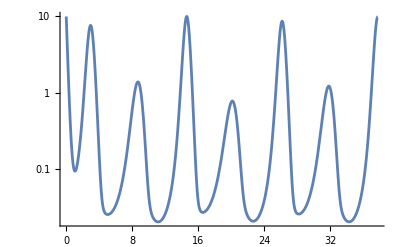

```mathematica
ParametricPlot3D[ySol[t],{t, 0 ,tEnd},
PlotPoints->1000,
PlotRange->All]
LogPlot[ySol[t]⟦3⟧,{t, 0 ,tEnd},
PlotPoints->100,
PlotRange->All]
```

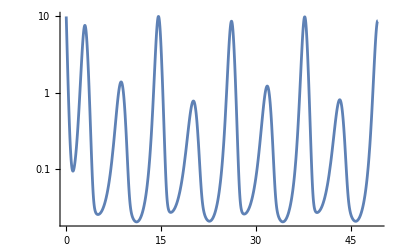

```mathematica
ParametricPlot3D[ySol[t],{t, 0 ,tEnd},
PlotPoints->1000,
PlotRange->All];
LogPlot[ySol[t]⟦3⟧,{t, 0 ,tEnd},
PlotPoints->100,
PlotRange->All]
```

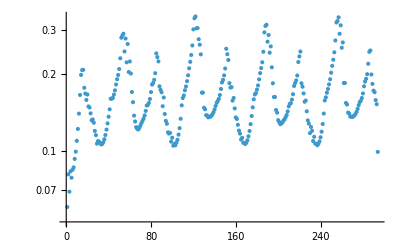

{0.,0.0739637,0.153073,0.229682,0.315384,0.396673,0.483719,0.572888,0.66921,0.772609,0.887165,1.01577,1.16528,1.34452,1.55149,1.76234,1.95688,2.1298,2.2929,2.45225,2.61324,2.7618,2.90723,3.04138,3.17377,3.29589,3.42244,3.54552,3.65351,3.76252,3.87018,3.97899,4.08478,4.1909,4.29736,4.40617,4.51824,4.63523,4.75837,4.8889,5.02767,5.1769,5.34241,5.49978,5.66459,5.83173,6.00827,6.19322,6.38725,6.58876,6.80405,7.047,7.33848,7.61866,7.89616,8.14158,8.388,8.61857,8.85936,9.06291,9.2939,9.47095,9.62362,9.77629,9.90716,10.0354,10.1559,10.276,10.395,10.5164,10.6402,10.7674,10.8972,11.03,11.1664,11.3081,11.4572,11.6086,11.7616,11.9201,12.0874,12.2677,12.4518,12.6405,12.8387,13.0665,13.3,13.5422,13.7231,13.9006,14.0695,14.222,14.383,14.5233,14.6544,14.7825,14.8987,15.0185,15.1429,15.2494,15.3649,15.4697,15.5767,15.6815,15.7889,15.8985,16.013,16.1339,16.2647,16.4109,16.5724,16.7354,16.9074,17.0847,17.2708,17.4663,17.6745,17.8956,18.1303,18.3844,18.6732,19.004,19.3325,19.6523,19.9457,20.2375,20.4926,20.7431,20.9176,21.0922,21.242,21.3896,21.5284,21.6664,21.8018,21.9376,22.0733,22.2103,22.3487,22.4895,22.6336,22.7821,22.9354,23.0916,23.2505,23.4142,23.5859,23.7691,23.9577,24.1531,24.3585,24.5918,24.8334,25.0818,25.2705,25.4526,25.625,25.789,25.9512,26.0992,26.2357,26.3687,26.4889,26.6119,26.7402,26.8471,26.9627,27.0706,27.1787,27.2847,27.392,27.5008,27.6131,27.7302,27.8542,27.9872,28.1309,28.286,28.4508,28.6182,28.7901,28.9678,29.1546,29.3524,29.5605,29.7782,30.0129,30.2841,30.602,30.9174,31.2019,31.4841,31.7355,31.9923,32.2211,32.4482,32.6129,32.7775,32.9229,33.0653,33.1978,33.3278,33.4549,33.5826,33.7114,33.8421,33.9746,34.1093,34.2467,34.3883,34.5361,34.6891,34.8422,35.,35.1646,35.3417,35.526,35.7138,35.909,36.1238,36.3627,36.6068,36.8011,36.9804,37.1486,37.31,37.4624,37.6111,37.7454,37.8751,37.9958,38.1276,38.2412,38.3558,38.4665,38.5762,38.6817,38.7875,38.8935,39.002,39.1141,39.2317,39.3572,39.4945,39.6491,39.8111,39.9787,40.1529,40.3337,40.5232,40.7236,40.9371,41.163,41.4037,41.6686,41.9817,42.308,42.649,42.9397,43.2645,43.5207,43.8025,43.9949,44.1616,44.3283,44.4751,44.6205,44.7587,44.8963,45.0317,45.1677,45.3039,45.4415,45.5806,45.7224,45.8677,46.018,46.173,46.3299,46.4903,46.6569,46.8341,47.0207,47.2115,47.4101,47.625,47.8758,48.1199,48.3296,48.5131,48.687,48.8626,49.0189,49.1756,49.3163,49.4506,49.5758,49.7145,49.8323,49.9161,50.}

```mathematica
ts=ySol["Coordinates"]⟦1⟧;
hs=Drop[ts-RotateRight[ts],1];
ListLogPlot[hs]
```

40

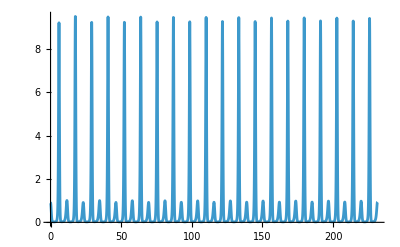

```mathematica
w=1; (* This is the winding #2 parametrs we found *)
n=0;
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==yVal,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>If[n++>w,"StopIntegration";tEnd=t]
}
];
n
ParametricPlot3D[ySol[t],{t, 0 ,tEnd},
PlotPoints->1000,
PlotRange->All];
Plot[ySol[t]⟦3⟧,{t, 0 ,tEnd},
PlotPoints->100,
PlotRange->All]
```

### Existing Code Fragments

#### Version 1

Right now we know how to go round a bunch of times recording stuff as we cross the Poincare section. I added the sensitivity computation.

-Graphics3D-

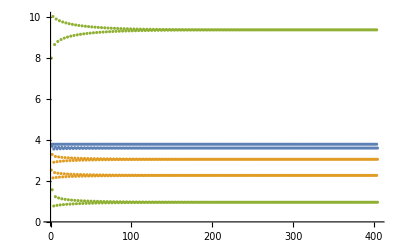

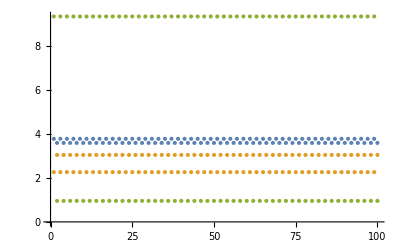

{{{3.78865,2.26831,9.36663},{{-0.363768,-4.28398,-0.356502},{0.132638,1.56202,0.129986},{-9.61282×10^-6,-0.0000235543,1.4671×10^-6}}},{{3.60131,3.0536,0.958366},{{-0.12543,-1.4772,-0.12293},{0.131688,1.55086,0.129059},{2.79438×10^-6,4.0592×10^-6,-7.65047×10^-7}}},{{3.78865,2.2683,9.36672},{{-0.363767,-4.284,-0.356504},{0.132633,1.56201,0.129987},{8.65902×10^-6,0.0000163852,-1.90835×10^-6}}},{{3.60131,3.05359,0.95834},{{-0.125436,-1.4772,-0.122927},{0.13169,1.55086,0.129058},{-3.08519×10^-6,-8.79263×10^-6,3.21116×10^-7}}}}

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
yJData=Reap[
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}
]]⟦2,1⟧;
ParametricPlot3D[ySol[t],{t, 0.95*TMax, TMax},PlotRange->All,PlotPoints->10^3]
ListPlot[yJData⟦All,1⟧ᵀ,PlotRange->All]
ListPlot[yJData⟦-100;;-1,1⟧ᵀ,PlotRange->All]
yJData⟦-4;;-1⟧
```

#### Version 2

I can do the data extraction in a different way. If we want.

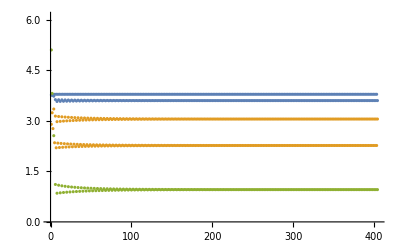

{{3.60131,3.05359,0.958342},{{1.24157,2.23782,-0.169391},{-1.30363,-2.34961,0.177864},{-0.000159545,-0.000201256,0.0000274521}}}

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={PData,{y[t],J[t]}})
}
];
PData=Partition[Flatten[PData],3+3^2];
PData=Table[yJs=PData⟦i⟧;
ys=yJs⟦1;;3⟧; Js=yJs⟦4;;3+3^2⟧;
{ys,Partition[Js,3]},{i,Length[PData]}];
yData=PData⟦All,1⟧;
ListPlot[yDataᵀ]
{yEnd, JEnd}=PData⟦-1⟧
```

```mathematica
MatrixForm[JEnd];
MatrixForm[JEndᵀ.JEnd];
MatrixForm[JEnd.JEndᵀ];
Eigenvalues[JEnd];
SingularValueList[JEnd,Tolerance->0]
```

{3.71885,0.0000506189,1.08826×10^-16}

#### Version 3

We also know how to go round once and stop the first time we cross the P-section.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=234; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={y[t],J[t]};"StopIntegration")
}
];
PData
```

{{3.77082,2.89763,5.10453},{{-0.0570967,1.85847,0.029455},{0.450972,-0.350306,-0.102516},{-3.23243,-3.22319,0.457328}}}

```mathematica
□^□
```

```mathematica
¶Thi
```

```mathematica
¶Th
```

```mathematica
The
```

## Rosseller System, Sensitivity, and Sections

We are going to build code and explore the behavior of the system on the standard section.

### Existing Code Fragments

#### Version 1

Right now we know how to go round a bunch of times recording stuff as we cross the Poincare section. I added the sensitivity computation.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
yJData=Reap[
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}
]]⟦2,1⟧;
ParametricPlot3D[ySol[t],{t, 0.95*TMax, TMax},PlotRange->All,PlotPoints->10^3]
ListPlot[yJData⟦All,1⟧ᵀ,PlotRange->All]
ListPlot[yJData⟦-100;;-1,1⟧ᵀ,PlotRange->All]
yJData⟦-4;;-1⟧
```

-Graphics3D-

-Graphics-

-Graphics-

{{{3.78865,2.26831,9.36663},{{-0.363768,-4.28398,-0.356502},{0.132638,1.56202,0.129986},{-9.61282×10^-6,-0.0000235543,1.4671×10^-6}}},{{3.60131,3.0536,0.958366},{{-0.12543,-1.4772,-0.12293},{0.131688,1.55086,0.129059},{2.79438×10^-6,4.0592×10^-6,-7.65047×10^-7}}},{{3.78865,2.2683,9.36672},{{-0.363767,-4.284,-0.356504},{0.132633,1.56201,0.129987},{8.65902×10^-6,0.0000163852,-1.90835×10^-6}}},{{3.60131,3.05359,0.95834},{{-0.125436,-1.4772,-0.122927},{0.13169,1.55086,0.129058},{-3.08519×10^-6,-8.79263×10^-6,3.21116×10^-7}}}}

#### Version 2

I can do the data extraction in a different way. If we want.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
PData={};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={PData,{y[t],J[t]}})
}
];
PData=Partition[Flatten[PData],3+3^2];
PData=Table[yJs=PData⟦i⟧;
ys=yJs⟦1;;3⟧; Js=yJs⟦4;;3+3^2⟧;
{ys,Partition[Js,3]},{i,Length[PData]}];
yData=PData⟦All,1⟧;
ListPlot[yDataᵀ]
{yEnd, JEnd}=PData⟦-1⟧
```

-Graphics-

{{3.60131,3.05359,0.958342},{{1.24157,2.23782,-0.169391},{-1.30363,-2.34961,0.177864},{-0.000159545,-0.000201256,0.0000274521}}}

```mathematica
MatrixForm[JEnd];
MatrixForm[JEndᵀ.JEnd];
MatrixForm[JEnd.JEndᵀ];
Eigenvalues[JEnd];
SingularValueList[JEnd,Tolerance->0]
```

{3.71885,0.0000506189,1.08826×10^-16}

#### Version 3

We also know how to go round once and stop the first time we cross the P-section.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=234; y0={-3,-4,5};
p={a,b,c}={0.2,0.2,3.81};
ySol=NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(PData={y[t],J[t]};"StopIntegration")
}
];
PData
```

{{3.77082,2.89763,5.10453},{{-0.0570967,1.85847,0.029455},{0.450972,-0.350306,-0.102516},{-3.23243,-3.22319,0.457328}}}

### Code Development

The plan is to build up code to recreate better versions of the images from Wiki.  For example, https://en.wikipedia.org/wiki/R%C3%B6ssler_attractor#Varying_a

### Basic ODE Solver Tests: Speed

Seeing if we can make the basic solve a tad faster. I do not think 5% is worth the fuss.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},{y,J},{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}];
]
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}];
]
AbsoluteTiming[
Quiet[NDSolveValue[{
y'[t]==f[p][y[t]],
J'[t]==df[p][y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},{},{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[{y[t],J[t]}]
}]];
]
```

{2.09434,Null}

{2.00506,Null}

{1.98554,Null}

The code might be faster as the more explicit x,y,z version of the code.  It might be faster with the parameters passed in to functions.  I think it will be faster if we do not do the sensitivity computation on the approach to asymptotic version.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=2340; y0={3,4,5};
p={a,b,c}={0.2,0.2,3.81};
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]==y0
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[y[t]]
}];
]
AbsoluteTiming[
NDSolveValue[{
y'[t]==f[p][y[t]],
y[0]==y0
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[p][y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>Sow[y[t]]
}];
]
```

{1.17311,Null}

{1.15986,Null}

It is faster but not as much faster as I might have hoped. I do not think changing the saving technique would change much.  It might get faster changing the ODE algorithm but I think that is getting a bit distracted.

If I really wanted this to be as fast as possible I would implement it in Julia with the update variables stored as static following the advice in the Julia documentation.  I think this would produce some real speed up.  I do not know how the Julia event handler would interact with the optimizations.

Conclusions: 1) Stick with Mathematica. 2) Drop the sensitivity Analysis for getting to the limit cycle. 3) Do not worry to much about the solver.

### Code Chunks

#### SetUpSection

Making it stop after “SetUpCount” crossings of standard section “z” at max.
Input: f as a suitable function, t0 IC 3-vector and and SetUpCount.  
Output: list of counter, end time, and final crossing point 3-vector.
I am not going to bother “typing” the variables.

```mathematica
SetUpSection[f_,y0_,SetUpCount_]:=Module[
{n=0,y,t,TMax=10^5,yOut,tOut=0.0},
NDSolveValue[{
y'[t]==f[y[t]],
y[0]==y0
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(
If[n++>SetUpCount,tOut=t;yOut=y[t];"StopIntegration"]
)
}];
{n,tOut,yOut}
]
```

Here is a timed test of the development version.

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
 p={0.2,0.2,3.81};
y0={3,4,5};
Table[
AbsoluteTiming[SetUpSection[f[p],y0,SetUpCount]],
{SetUpCount,{100,101,1000,1001,1004,2000,2002}}]
```

Has it converged?

Could we help it converge faster?

Is there any danger in helping it converge faster?

#### StepRoundSection

Once we have found a limit cycle we need to make the solver step round the limit cycle until it gets back to the same point and save a list of crossing points and sensitivities?  I do not think we have any idea right now about how close a return point needs to be:  we decided to call the return tolerance “DyTol”.  For safety we need to make a maximum number of loops: we decided to call that MaxCounts. It needs to take as input the function, the sensitivity function, and the initial point.  I think we decided it should return a list of counts, times, points, and sensitivities.

```mathematica
StepRoundSection[{f_,df_},y0_,DyTol_, MaxCounts_]:=Module[
{n=0,y,J,t,TMax=10^4,yOut,tOut=0.0},
Reap[NDSolveValue[{
y'[t]==f[y[t]],
J'[t]==df[y[t]].J[t],
y[0]==y0,
J[0]==IdentityMatrix[3]
},y,{t, 0, TMax},
Method->{"EventLocator",
"Event":>f[y[t]]⟦3⟧,
"Direction"->-1,
"EventAction":>(
Sow[{n++,t,y[t],J[t]}];
If[Or[Norm[y[t]-y0]<DyTol, n>MaxCounts],"StopIntegration"]
)
}]]⟦2,1⟧
]
```

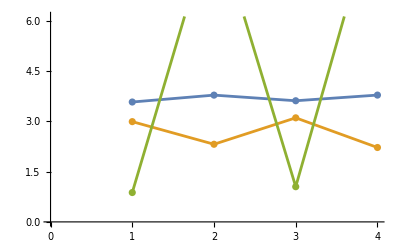

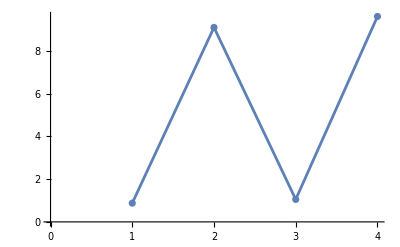

Part::take: Cannot take positions 1 through 500 in {0.877273,9.09419,1.05157,9.60624}.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 1;;500;;2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListPlot::lpn: {0.877273,9.09419,1.05157,9.60624}⟦1;;500;;2⟧ is not a list of numbers or pairs of numbers.

ListPlot[{0.877273,9.09419,1.05157,9.60624}⟦1;;500;;2⟧,Joined→True,Mesh→All]

```mathematica
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x + a y, b +z (x-c)}
df[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
 p={0.2,0.2,3.81};
y0={3,4,5};
SetUpCount=25;
MaxCounts=500;
{n,t,ySection}=SetUpSection[f[p],y0,SetUpCount];
DyTol=0.03;
Data=StepRoundSection[{f[p],df[p]},ySection,DyTol,MaxCounts];
xyzs=Data⟦All,3⟧;
ListPlot[
xyzsᵀ,
Joined->True,Mesh->All
]
zs=xyzs⟦All,3⟧;
ListPlot[zs,Joined->True,Mesh->All]
ListPlot[zs⟦1;;MaxCounts;;2⟧,Joined->True,Mesh->All]
```

Has it converged?

How/where do we put a stopping condition in our code?

What should our tolerance be?

Is there any danger in setting a low tolerance?

Does it matter if it is a relative or absolute tolerance?